```mathematica
FullSimplify[Integrate[Log[4 Sin[k/2]^2+m^2],{k,-π,π}],{m∈Reals,m>0}]
```

2 π Log[1/2 (2+m (m+√(4+m^2)))]

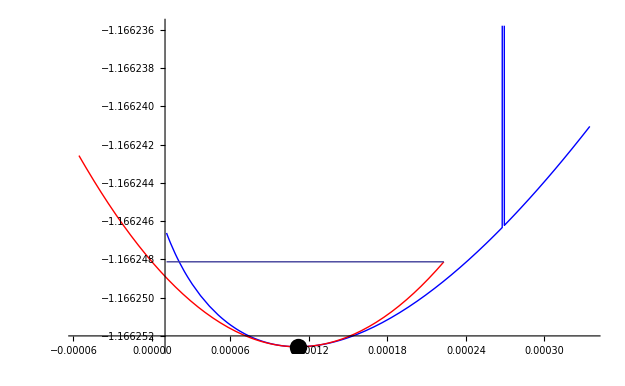

```mathematica
V[ϕ_,λ_]:=-1/(4 π^2)NIntegrate[Log[4 Sin[kx/2]^2+4 Sin[ky/2]^2+ϕ],{kx,-π,π},{ky,-π,π}]+ϕ/λ;
dV[ϕ_,λ_]:=-1/(4 π^2)NIntegrate[1/(4 Sin[kx/2]^2+4 Sin[ky/2]^2+ϕ),{kx,-π,π},{ky,-π,π}]+1/λ;
d2V[ϕ_]:=1/(4 π^2)NIntegrate[1/(4 Sin[kx/2]^2+4 Sin[ky/2]^2+ϕ)^2,{kx,-π,π},{ky,-π,π}];
d2V0[ϕ_]:=1/(4π ϕ);
ϕmin[λ_]:=32 Exp[-(4π)/λ];
λ0=1.0;
ϕ0=ϕmin[λ0];
V0=V[ϕ0,λ0];
Gr1=Plot[V[ϕ,λ0],{ϕ,0.1 ϕ0,3 ϕ0},PlotStyle->{Blue}];
Gr3=Plot[V0+ 1/2 d2V0[ϕ0] (ϕ-ϕ0)^2,{ϕ,-0.5 ϕ0,2 ϕ0},PlotStyle->{Red}];
Gr4=Plot[V0+1/2 d2V0[ϕ0] ϕ0^2  Exp[-1/2 d2V0[ϕ0] (ϕ-ϕ0)^2],{ϕ,0.1 ϕ0,2ϕ0}];
Gr2=Graphics[{PointSize[0.02],Point[{ϕ0,V0}]}];
Print[Show[Gr1,Gr2,Gr3,Gr4,PlotRange->All]]
```

```mathematica
FullSimplify
```

```mathematica
V[ϕ_]:=-Log[a+ϕ]
```

```mathematica
Series[-Log[a-x],{x,0,10}]
```

-Log[a]+x/a+x^2/(2 a^2)+x^3/(3 a^3)+x^4/(4 a^4)+x^5/(5 a^5)+x^6/(6 a^6)+x^7/(7 a^7)+x^8/(8 a^8)+x^9/(9 a^9)+x^10/(10 a^10)+O[x]^11

```mathematica
Log[]
```